```mathematica
We start testing the polynomials assuming that the middle poinst are (b+c)/2  and (a+b)/2
Expand[((b+c)/2-(a+b)/2)^2 ]/ Integrate[(x-b)^2,{x,(a+b)/2,(b+c)/2}]
```

```mathematica
a = .
```

```mathematica
b = .
```

```mathematica
Expand[((b+c)/2-(a+b)/2)^2 ]/ Integrate[(x-b)^2,{x,(a+b)/2,(b+c)/2}]
```

(9/4-(3 a)/2+a^2/4)/(9/8-a^3/24-(9 b)/8+(a^2 b)/8+(3 b^2)/8-(a b^2)/8)

```mathematica
I realized the that my initial assumtion doesn't work therefore, I assume now that b = (a+c)/2
```

```mathematica
Factor[(c-a)^1 ]/ Integrate[(1)^2,{x,a,c}]
```

1

```mathematica
Factor[(c-a)^2 ]/ Integrate[((x-(a+c)/2))^2,{x,a,c}]
```

-12/(a-c)

```mathematica
Factor[(c-a)^3 ]/ Integrate[(((x-(a+c)/2)^2-1/12 (a-c)^2))^2,{x,a,c}]
```

180/(a-c)^2

```mathematica
Great Success!
```

```mathematica
Factor[Table[1/(2^l l!)  D[(x^2-1)^l,{x,l}],{l,0,2}]]
```

{1,x,1/2 (-1+3 x^2)}

```mathematica
Factor[Table[1/(2^l l!)  D[((x+b)^2-1)^l,{x,l}],{l,0,2}]]
```

{1,b+x,1/2 (-1+3 b^2+6 b x+3 x^2)}

```mathematica
Factor[(c-a)^3 ]/ Integrate[(({1,x-(a+c)/2,1/2 (-1+3 (x-(a+c)/2)^2)}))^2,{x,a,c}]
```

{-(a-c)^3/(-a+c),12,-(a-c)^3/(-a/4+a^3/8-(9 a^5)/320+c/4-(3 a^2 c)/8+(9 a^4 c)/64+(3 a c^2)/8-(9 a^3 c^2)/32-c^3/8+(9 a^2 c^3)/32-(9 a c^4)/64+(9 c^5)/320)}

```mathematica
a = 1
c = 3
(-(a-c)^3)/(-a/4+a^3/8-(9 a^5)/320+c/4-(3 a^2 c)/8+(9 a^4 c)/64+(3 a c^2)/8-(9 a^3 c^2)/32-c^3/8+(9 a^2 c^3)/32-(9 a c^4)/64+(9 c^5)/320)
```

1

3

20

```mathematica
(180)/(c-a)^2
```

45

```mathematica
Integrate [((x-0.5)^2-1/12 (1)^2)(x-(0.5)^2-1/12 (1)^2),{x,-1,1}]
```

-1.

```mathematica
Integrate[(1/2 (-1+3 x^2))(1/2 (-1+3 x^2)),{x,-1,1}]
```

2/5

```mathematica
Integrate[(1/2 (-1+3 x^2))(x),{x,-1,1}]
```

0

```mathematica
Integrate[((x-b)^2-1/12 (c-a)^2)(x-b),{x,-1,1}]
```

-(4 b)/3-2 b^3

```mathematica
LegendreP[10,x]
```

1/256 (-63+3465 x^2-30030 x^4+90090 x^6-109395 x^8+46189 x^10)

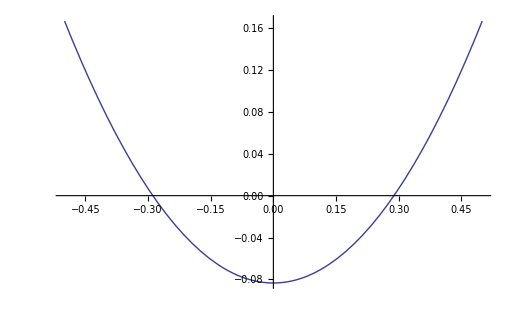

```mathematica
Plot[(x)^2-1/12(1)^2,{x,-0.50,0.50}]
```

```mathematica
Table[1/l!(b-a)^l D[(x-a)^l (x-b)^l,{x,l}],{l,0,2}]
```

{1,(-a+b) (-a-b+2 x),1/2 (-a+b)^2 (2 (-a+x)^2+8 (-a+x) (-b+x)+2 (-b+x)^2)}

```mathematica
180/12
```

15